```mathematica
(*The first point is from 1007.2580*)
a={0.2824,0.2556,0.2490,0.2425,0.2361,0.2297,0.2235,0.2173,0.2142,0.2112,0.2052,0.1994,0.1937,0.1908,0.1881,0.1826,0.1773,0.1722,0.1672,0.1625,0.1579,0.1535,0.1493,0.1453,0.1416,0.1379,0.1345,0.1312,0.1280,0.1249,0.1110};
beta={3.45,3.490,3.500,3.510,3.520,3.530,3.540,3.550,3.555,3.560,3.570,3.580,3.590,3.595,3.600,3.610,3.620,3.630,3.640,3.650,3.660,3.670,3.680,3.690,3.700,3.710,3.720,3.730,3.740,3.750,3.800};
ms={0.157,0.132,0.126,0.121,0.116,0.111,0.10643,0.10200,0.09987,0.09779,0.09378,0.08998,0.08638,0.08465,0.08296,0.07973,0.07668,0.07381,0.07110,0.06854,0.06615,0.06390,0.06179,0.05982,0.05797,0.05624,0.05462,0.05309,0.05166,0.05030,0.04445};
```

```mathematica
betaa=Interpolation[Transpose[{a,beta}]];
msa=Interpolation[Transpose[{a,ms}]];
```

```mathematica
aval=0.207349643812;
betaa[aval]
msa[aval]
```

3.5664

0.0952001

```mathematica
abeta = Interpolation[Transpose[{beta, a}]];
betaval = 3.45887;
```

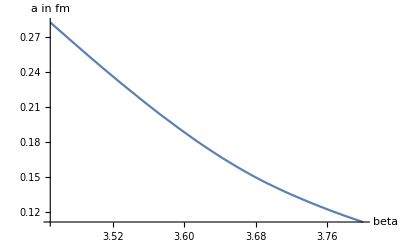

```mathematica
Plot[abeta[beta], {beta, 3.45, 3.8 }, AxesLabel->{HoldForm[beta],HoldForm[a in fm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
T[x_] := (1/(abeta[x] 6))/5.068
```

```mathematica
T[3.45]
```

0.116452

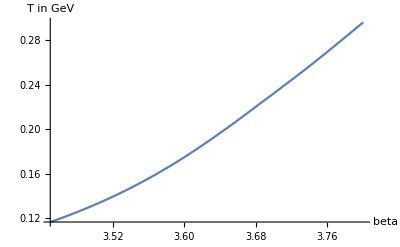

```mathematica
Plot[(1/(abeta[beta] 6))/5.068, {beta, 3.45, 3.8 }, AxesLabel->{HoldForm[beta],HoldForm[T in GeV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
B[n_, beta_] := (2 π 3/2 n)/(24^2 abeta[beta]^2)
```

```mathematica
B[6]
```

1.28452

```mathematica
betaslist = {3.45887,3.45887,3.45887,3.45887,3.45887,3.45887,3.45887,3.45887,3.47193,3.47193,3.47193,3.47193,3.47193,3.47193,3.47193,3.47193,3.47519,3.47519,3.47519,3.47519,3.47519,3.47519,3.47519,3.47519,3.47999,3.47999,3.47999,3.47999,3.47999,3.47999,3.47999,3.47999,3.48242,3.48242,3.48242,3.48242,3.48242,3.48242,3.48242,3.48242,3.4836,3.4836,3.4836,3.4836,3.4836,3.4836,3.4836,3.4836,3.48486,3.48486,3.48486,3.48486,3.48486,3.48486,3.48486,3.48486,3.48548,3.48548,3.48548,3.48548,3.48548,3.48548,3.48548,3.48548,3.4898,3.4898,3.4898,3.4898,3.4898,3.4898,3.4898,3.4898,3.4911,3.4911,3.4911,3.4911,3.4911,3.4911,3.4911,3.4911,3.4923,3.4923,3.4923,3.4923,3.4923,3.4923,3.4923,3.4923,3.49486,3.49486,3.49486,3.49486,3.49486,3.49486,3.49486,3.49486,3.49488,3.49488,3.49488,3.49488,3.49488,3.49488,3.49488,3.49488,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.4949,3.49969,3.49969,3.49969,3.49969,3.49969,3.49969,3.49969,3.49969,3.5026,3.5026,3.5026,3.5026,3.5026,3.5026,3.5026,3.5026,3.5027,3.5027,3.5027,3.5027,3.5027,3.5027,3.5027,3.5027,3.5066,3.5066,3.5066,3.5066,3.5066,3.5066,3.5066,3.5066,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.50796,3.5107,3.5107,3.5107,3.5107,3.5107,3.5107,3.5107,3.5107,3.51479,3.51479,3.51479,3.51479,3.51479,3.51479,3.51479,3.51479,3.5148,3.5148,3.5148,3.5148,3.5148,3.5148,3.5148,3.5148,3.5162,3.5162,3.5162,3.5162,3.5162,3.5162,3.5162,3.5162,3.519,3.519,3.519,3.519,3.519,3.519,3.519,3.519,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.52179,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5275,3.5303,3.5303,3.5303,3.5303,3.5303,3.5303,3.5303,3.5303,3.53075,3.53075,3.53075,3.53075,3.53075,3.53075,3.53075,3.53075,3.53638,3.53638,3.53638,3.53638,3.53638,3.53638,3.53638,3.53638,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5364,3.5457,3.5457,3.5457,3.5457,3.5457,3.5457,3.5457,3.5457,3.54798,3.54798,3.54798,3.54798,3.54798,3.54798,3.54798,3.54798,3.5503,3.5503,3.5503,3.5503,3.5503,3.5503,3.5503,3.5503,3.55189,3.55189,3.55189,3.55189,3.55189,3.55189,3.55189,3.55189,3.5519,3.5519,3.5519,3.5519,3.5519,3.5519,3.5519,3.5519,3.5551,3.5551,3.5551,3.5551,3.5551,3.5551,3.5551,3.5551,3.5601,3.5601,3.5601,3.5601,3.5601,3.5601,3.5601,3.5601,3.5651,3.5651,3.5651,3.5651,3.5651,3.5651,3.5651,3.5651,3.5664,3.5664,3.5664,3.5664,3.5664,3.5664,3.5664,3.5664,3.56855,3.56855,3.56855,3.56855,3.56855,3.56855,3.56855,3.56855,3.5686,3.5686,3.5686,3.5686,3.5686,3.5686,3.5686,3.5686,3.5703,3.5703,3.5703,3.5703,3.5703,3.5703,3.5703,3.5703,3.5757,3.5757,3.5757,3.5757,3.5757,3.5757,3.5757,3.5757,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.58696,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.587,3.6069,3.6069,3.6069,3.6069,3.6069,3.6069,3.6069,3.6069,3.60952,3.60952,3.60952,3.60952,3.60952,3.60952,3.60952,3.60952,3.6178,3.6178,3.6178,3.6178,3.6178,3.6178,3.6178,3.6178,3.6248,3.6248,3.6248,3.6248,3.6248,3.6248,3.6248,3.6248,3.6296,3.6296,3.6296,3.6296,3.6296,3.6296,3.6296,3.6296,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.6562,3.7927,3.7927,3.7927,3.7927,3.7927,3.7927,3.7927,3.7927};
```

```mathematica
alist = Map[abeta, betaslist]
```

{0.276459,0.276459,0.276459,0.276459,0.276459,0.276459,0.276459,0.276459,0.267683,0.267683,0.267683,0.267683,0.267683,0.267683,0.267683,0.267683,0.265494,0.265494,0.265494,0.265494,0.265494,0.265494,0.265494,0.265494,0.262277,0.262277,0.262277,0.262277,0.262277,0.262277,0.262277,0.262277,0.260651,0.260651,0.260651,0.260651,0.260651,0.260651,0.260651,0.260651,0.259863,0.259863,0.259863,0.259863,0.259863,0.259863,0.259863,0.259863,0.259022,0.259022,0.259022,0.259022,0.259022,0.259022,0.259022,0.259022,0.258608,0.258608,0.258608,0.258608,0.258608,0.258608,0.258608,0.258608,0.255733,0.255733,0.255733,0.255733,0.255733,0.255733,0.255733,0.255733,0.254869,0.254869,0.254869,0.254869,0.254869,0.254869,0.254869,0.254869,0.254073,0.254073,0.254073,0.254073,0.254073,0.254073,0.254073,0.254073,0.25238,0.25238,0.25238,0.25238,0.25238,0.25238,0.25238,0.25238,0.252367,0.252367,0.252367,0.252367,0.252367,0.252367,0.252367,0.252367,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.252354,0.249203,0.249203,0.249203,0.249203,0.249203,0.249203,0.249203,0.249203,0.2473,0.2473,0.2473,0.2473,0.2473,0.2473,0.2473,0.2473,0.247235,0.247235,0.247235,0.247235,0.247235,0.247235,0.247235,0.247235,0.244699,0.244699,0.244699,0.244699,0.244699,0.244699,0.244699,0.244699,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.243818,0.24205,0.24205,0.24205,0.24205,0.24205,0.24205,0.24205,0.24205,0.239428,0.239428,0.239428,0.239428,0.239428,0.239428,0.239428,0.239428,0.239422,0.239422,0.239422,0.239422,0.239422,0.239422,0.239422,0.239422,0.238527,0.238527,0.238527,0.238527,0.238527,0.238527,0.238527,0.238527,0.236738,0.236738,0.236738,0.236738,0.236738,0.236738,0.236738,0.236738,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.234949,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.231289,0.229512,0.229512,0.229512,0.229512,0.229512,0.229512,0.229512,0.229512,0.229231,0.229231,0.229231,0.229231,0.229231,0.229231,0.229231,0.229231,0.225734,0.225734,0.225734,0.225734,0.225734,0.225734,0.225734,0.225734,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.225722,0.219966,0.219966,0.219966,0.219966,0.219966,0.219966,0.219966,0.219966,0.218552,0.218552,0.218552,0.218552,0.218552,0.218552,0.218552,0.218552,0.217113,0.217113,0.217113,0.217113,0.217113,0.217113,0.217113,0.217113,0.216121,0.216121,0.216121,0.216121,0.216121,0.216121,0.216121,0.216121,0.216115,0.216115,0.216115,0.216115,0.216115,0.216115,0.216115,0.216115,0.214139,0.214139,0.214139,0.214139,0.214139,0.214139,0.214139,0.214139,0.21114,0.21114,0.21114,0.21114,0.21114,0.21114,0.21114,0.21114,0.20813,0.20813,0.20813,0.20813,0.20813,0.20813,0.20813,0.20813,0.207349,0.207349,0.207349,0.207349,0.207349,0.207349,0.207349,0.207349,0.206063,0.206063,0.206063,0.206063,0.206063,0.206063,0.206063,0.206063,0.206033,0.206033,0.206033,0.206033,0.206033,0.206033,0.206033,0.206033,0.205024,0.205024,0.205024,0.205024,0.205024,0.205024,0.205024,0.205024,0.201876,0.201876,0.201876,0.201876,0.201876,0.201876,0.201876,0.201876,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195439,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.195416,0.184302,0.184302,0.184302,0.184302,0.184302,0.184302,0.184302,0.184302,0.182863,0.182863,0.182863,0.182863,0.182863,0.182863,0.182863,0.182863,0.178449,0.178449,0.178449,0.178449,0.178449,0.178449,0.178449,0.178449,0.174833,0.174833,0.174833,0.174833,0.174833,0.174833,0.174833,0.174833,0.172401,0.172401,0.172401,0.172401,0.172401,0.172401,0.172401,0.172401,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.15963,0.112855,0.112855,0.112855,0.112855,0.112855,0.112855,0.112855,0.112855}